```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

```mathematica
norms
```

Single run plots

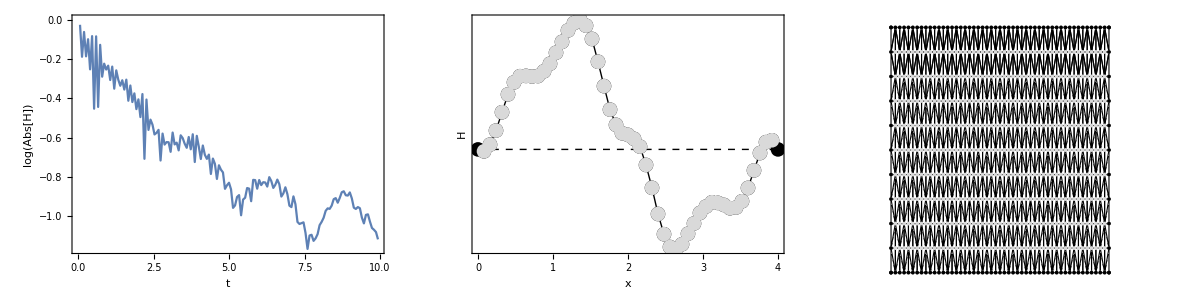

16.000000 0.500000

```mathematica
filebase="data/nr8";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]}}]
lst[[-1]]
```

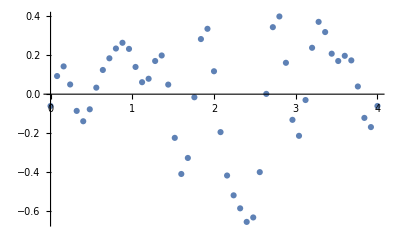

0.4

InterpolatingFunction[…]

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,0.0860615,-0.231326,0.0801865,-0.156175}

{-0.000136031,0.267982,-0.261773,-0.135942,0.167666}

-0.000136031

```mathematica
ListPlot[mesh[[1,bottom]]]
Max[mesh[[1,bottom,2]]]
h=Interpolation[mesh[[1,bottom]]]
Table[NIntegrate[h[x]*Sin[n*2*Pi*x/length],{x,0,length}],{n,0,4}]
Table[NIntegrate[h[x]*Cos[n*2*Pi*x/length],{x,0,length}],{n,0,4}]
NIntegrate[h[x],{x,0,length}]
```

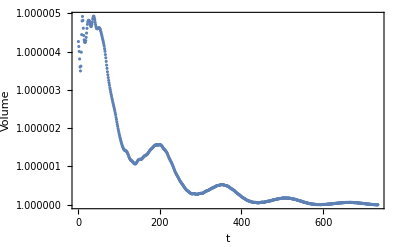

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,2]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Table[Pi*n/length,{n,1,20}]
frequencies=2*(980*modes*Tanh[height*modes]*(1+72/980*modes^2))^(1/2)/(2*Pi)
modes2=Table[Pi*n/length,{n,1,20}]
frequencies2=2*(980*modes2*Tanh[height*modes2]*(1+72/980*modes2^2))^(1/2)/(2*Pi)
```

{0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319,7.06858,7.85398,8.63938,9.42478,10.2102,10.9956,11.781,12.5664,13.3518,14.1372,14.9226,15.708}

{5.51932,10.9922,16.5031,22.2161,28.2768,34.7764,41.7591,49.2379,57.2083,65.6567,74.5655,83.9163,93.691,103.873,114.446,125.396,136.71,148.377,160.385,172.725}

{0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319,7.06858,7.85398,8.63938,9.42478,10.2102,10.9956,11.781,12.5664,13.3518,14.1372,14.9226,15.708}

{5.51932,10.9922,16.5031,22.2161,28.2768,34.7764,41.7591,49.2379,57.2083,65.6567,74.5655,83.9163,93.691,103.873,114.446,125.396,136.71,148.377,160.385,172.725}

Generate box substrate

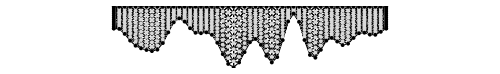

```mathematica
filebase="data/rectanglerandom";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-1;
mesh2=mesh[[m]];
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]
```

```mathematica
modes=ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate modes"][[1]]+1]]]];
smodes=Length[modes]/2;
subss=ConstantArray[0.,{smodes,smodes}]
subsc=Normal[SparseArray[Table[{i,1}->modes[[i]],{i,1,smodes}],{smodes,smodes}]]
subcs=ConstantArray[0.,{smodes,smodes}]
subcc=Normal[SparseArray[Table[{i,1}->modes[[smodes+i]],{i,1,smodes}],{smodes,smodes}]]
file=OpenWrite["boxsubstrate.dat"]
WriteString[file,smodes]
WriteString[file,"\n"]
Do[Do[WriteString[file,subss[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subsc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcs[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Close[file]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{{0.243232,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.084095,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.00397416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.395668,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.0156858,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.212189,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.0777383,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.19681,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.192743,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.0315948,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.271088,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.252703,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.381862,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.135099,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.0699322,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.292892,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.355393,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.101071,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.130175,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

OutputStream[…]

boxsubstrate.dat

Animation

```mathematica
m0=Length[mesh]-500;
m1=Length[mesh];
If[!DirectoryQ["rectangleanimation"],CreateDirectory["rectangleanimation"]];
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotStyle->{Directive[AbsoluteThickness[1],LightGray],Directive[AbsoluteThickness[2],Black]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]]},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(height+2)/(length+2),PlotRange->{{-1,length+1},{-1,height+1}}]}}];
Export["rectangleanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

Periodic sweep plots

sweeps/nr11

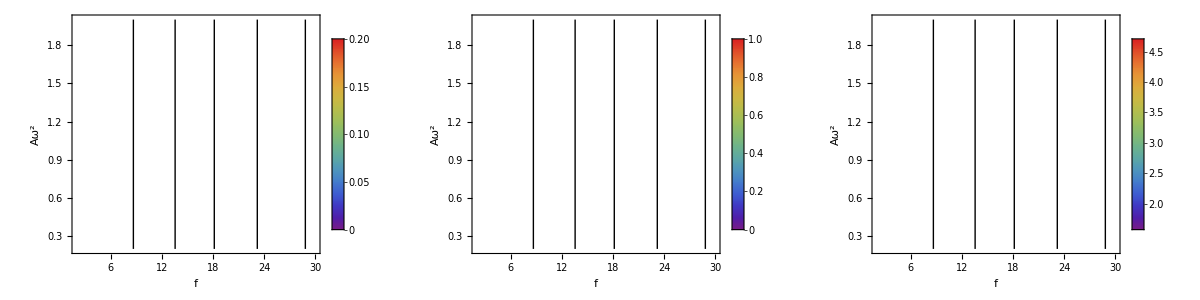

```mathematica
filebase="sweeps/nr11"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

```mathematica
2*Pi/4*3/2.
2*2*Pi/length*5/4.
2*Pi/4*4/2.
```

2.35619

3.92699

3.14159

```mathematica
modes
frequencies
```

{0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319,7.06858,7.85398,8.63938,9.42478,10.2102,10.9956,11.781,12.5664,13.3518,14.1372,14.9226,15.708}

{8.64676,13.5484,18.1475,23.1977,28.8395,35.0902,41.9305,49.33,57.2571,65.6822,74.5787,83.9231,93.6945,103.874,114.447,125.396,136.71,148.377,160.385,172.725}

```mathematica
height
```

0.5

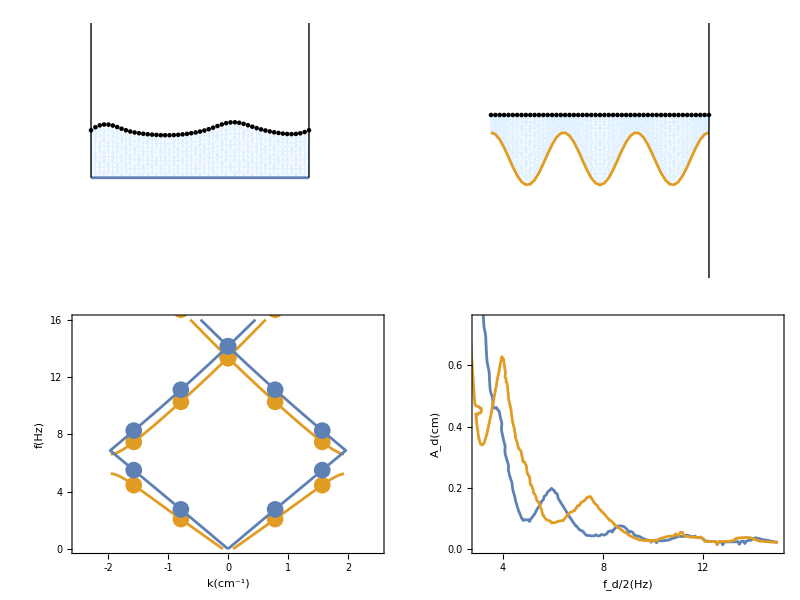

plots/periodicrectanglegap.pdf

```mathematica
gap=2*Pi/length*5/4;
ks=2*gap;
hs=0.3;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-2,2,1}],Table[{i,""},{i,-2,2,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]],ListPlot[Join[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,ks/2,Pi/length}]],Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,-ks/2,-Pi/length}]]],Joined->False,Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[PointSize[0.04],ColorData[97,"ColorList"][[2]]]],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-2,2,1}],Table[{i,""},{i,-2,2,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]]];
filebases={"sweeps/sr3","sweeps/sr4"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];p3=Show@@Table[ContourPlot[interpolations[f,a][[i]],{f,2.63,15},{a,0.000552,1.8},Contours->{0.0},PlotRange->{{3,15},{0,0.75}},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.6,0.2}],Table[{i,""},{i,0,0.6,0.2}]},{Table[{i,i},{i,4,14,2}],Table[{i,""},{i,4,14,2}]}}],{i,1,Length[sweeps]}];
filebase="data/rectangleperiodic";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,1.75},{0,2.0}}],Line[{{length,-1.75},{length,2.0}}]}];
filebase="data/rectanglehomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-100;
mesh2=mesh[[m]];
p4=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh2[[All,2]]]-Min[mesh2[[All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh2[[All,2]]],1+Max[mesh2[[All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,2.0}}],Line[{{length,0},{length,2.0}}]}];
filebase="sweeps/sa1";
fsweeps=Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}];
p5=ListPlot[Table[{1.75*i/100,MinimalBy[Cases[fsweeps[[All,i]],u_/;u[[4]]>0],#[[2]]&][[1,2]]*980/(2*Pi*16)^2},{i,1,100}],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],AspectRatio->1,LabelStyle->Directive[14,Black],FrameLabel->{Subscript[A,s],Subsuperscript[A,d,c]},ImageSize->150,PlotStyle->Directive[Black],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.1,0.05}],Table[{i,""},{i,0,0.1,0.05}]},{Table[{i,PaddedForm[i,{2,2}]},{i,0,1.75,0.75}],Table[{i,""},{i,0,1.75,0.75}]}}];
filebase="sweeps/sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p5=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->150,AspectRatio->1,PlotRange->{5,8},PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[4]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[5]]]}];
p=Grid[{{p4,p2},{p1,Show[p3,Epilog->Inset[p5,{10,0.4}]]}}]
Export["plots/periodicrectanglegap.pdf",p]
```

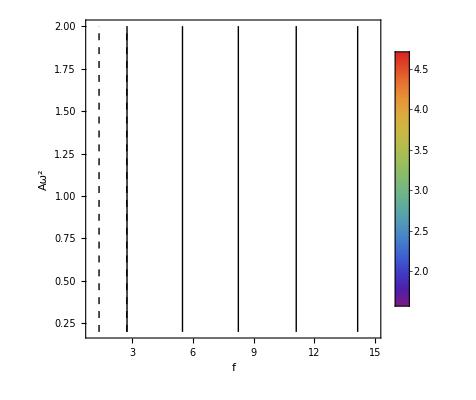
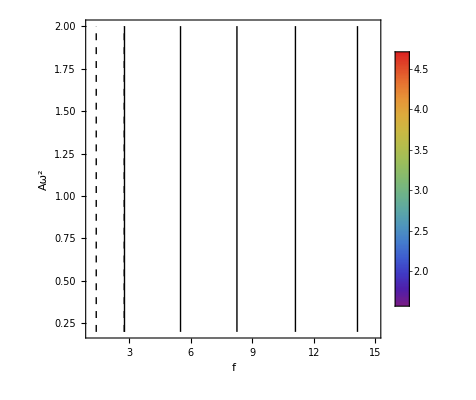

```mathematica
filebases={"sweeps/nr8","sweeps/nr9"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}]
```

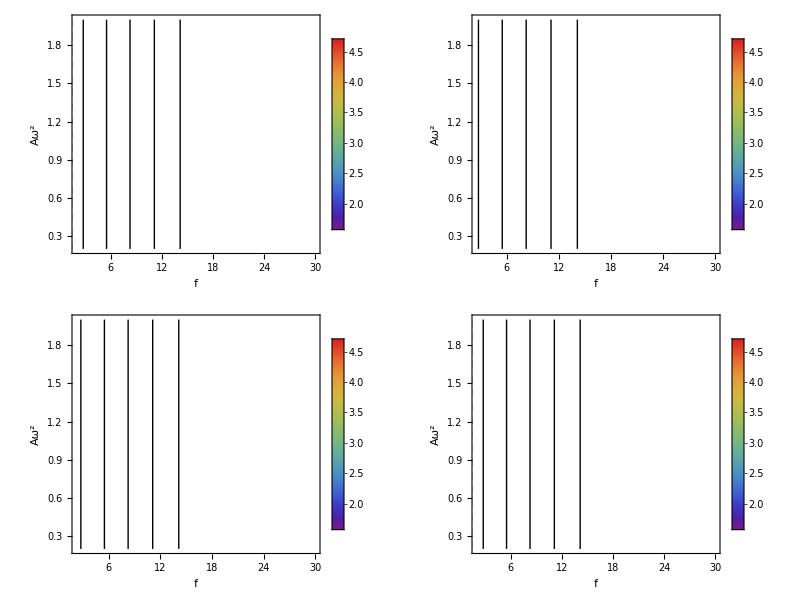

plots/modes.pdf

```mathematica
filebases={"sweeps/nr8","sweeps/nr9"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]],#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
filebases={"sweeps/nr10","sweeps/nr11"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Table[rasterizeBackground[ListDensityPlot[{#[[1]],#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
p=Grid[Transpose[{p1,p2}]]
Export["plots/modes.pdf",p]
```

Random substrates

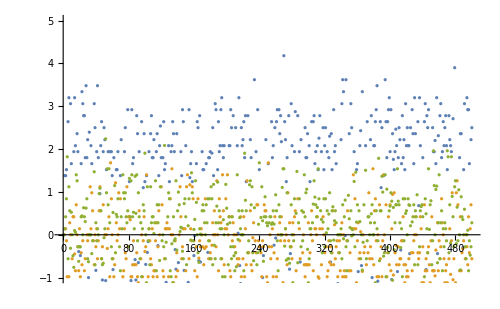

{52.,124.,453.,470.,222.,100.,475.,471.,5.,386.,240.,447.,409.,270.,269.,54.,312.,56.,370.,286.,38.,358.,157.,460.,394.,295.,213.,90.,84.,73.,16.,88.,390.,81.,229.,307.,162.,138.,113.,83.,17.,480.,356.,189.,199.,184.,228.,454.,63.,457.,231.,107.,479.,243.,181.,119.,103.,7.,268.,45.,298.,396.,456.,484.,391.,141.,401.,326.,129.,53.,297.,274.,158.,92.,76.,74.,44.,433.,260.,349.,476.,487.,247.,308.,321.,313.,182.,179.,130.,75.,67.,29.,4.,319.,443.,422.,289.,283.,177.,154.,149.,418.,416.,345.,223.,450.,410.,402.,163.,148.,306.,429.,423.,411.,408.,407.,360.,230.,175.,98.,55.,171.,473.,449.,378.,368.,342.,309.,279.,264.,142.,117.,115.,439.,424.,400.,188.,438.,330.,482.,404.,311.,234.,25.,28.,200.,491.,420.,352.,329.,315.,224.,219.,172.,140.,389.,362.,170.,463.,437.,431.,399.,388.,383.,333.,323.,292.,261.,257.,215.,191.,99.,79.,46.,8.,294.,86.,10.,61.,285.,89.,419.,444.,377.,325.,65.,23.,477.,440.,432.,428.,374.,344.,310.,296.,254.,253.,248.,150.,110.,85.,71.,22.,3.,488.,373.,66.,265.,246.,207.,203.,135.,128.,109.,93.,82.,77.,26.,242.,216.,350.,316.,161.,489.,196.,332.,244.,363.,27.,427.,359.,318.,500.,459.,406.,376.,288.,256.,252.,249.,204.,190.,187.,176.,112.,108.,78.,57.,173.,467.,462.,412.,334.,305.,116.,95.,40.,381.,258.,255.,239.,201.,425.,250.,153.,144.,351.,145.,468.,465.,445.,384.,302.,272.,194.,192.,105.,97.,87.,2.,414.,340.,324.,303.,217.,167.,72.,51.,42.,448.,160.,354.,495.,14.,143.,15.,322.,111.,168.,1.,24.,494.,490.,485.,455.,421.,380.,375.,365.,339.,337.,336.,280.,267.,220.,218.,197.,174.,164.,122.,43.,34.,32.,11.,379.,355.,266.,169.,101.,33.,353.,50.,343.,137.,214.,331.,156.,497.,469.,452.,417.,327.,293.,262.,227.,178.,136.,104.,41.,36.,483.,385.,372.,348.,282.,159.,121.,91.,367.,126.,474.,481.,133.,185.,271.,466.,492.,346.,320.,291.,278.,205.,123.,59.,21.,20.,18.,499.,478.,436.,357.,208.,80.,69.,397.,413.,9.,299.,405.,139.,241.,146.,317.,472.,446.,398.,393.,338.,328.,232.,226.,211.,64.,238.,165.,35.,498.,209.,12.,392.,94.,493.,461.,371.,364.,301.,276.,206.,186.,180.,147.,125.,60.,47.,30.,6.,341.,275.,193.,273.,118.,387.,233.,19.,245.,31.,166.,287.,458.,277.,49.,451.,434.,430.,237.,183.,151.,106.,48.,202.,39.,212.,13.,486.,366.,210.,496.,464.,347.,221.,114.,70.,263.,131.,132.,442.,415.,395.,198.,195.,96.,403.,382.,134.,300.,281.,102.,361.,314.,236.,120.,290.,37.,304.,284.,259.,68.}

{379.,133.,355.,201.,195.,392.,102.,482.,188.,64.,33.,158.,151.,120.,78.,143.,45.,275.,68.,481.,374.,476.,35.,405.,403.,159.,131.,165.,463.,357.,382.,287.,191.,174.,70.,59.,199.,499.,483.,442.,400.,395.,246.,238.,237.,121.,49.,387.,16.,304.,284.,381.,196.,185.,93.,46.,348.,330.,248.,247.,229.,117.,44.,36.,221.,12.,496.,486.,451.,437.,431.,416.,398.,318.,311.,267.,217.,206.,203.,144.,80.,56.,192.,99.,13.,283.,259.,81.,82.,458.,341.,193.,361.,281.,277.,208.,464.,265.,233.,183.,114.,65.,8.,300.,332.,314.,198.,69.,473.,438.,402.,358.,353.,308.,289.,256.,223.,169.,149.,147.,128.,126.,109.,55.,34.,309.,272.,156.,41.,20.,356.,354.,200.,130.,125.,105.,75.,3.,2.,498.,317.,364.,430.,385.,343.,340.,282.,263.,212.,202.,186.,39.,31.,9.,465.,303.,493.,393.,219.,209.,142.,118.,96.,51.,17.,432.,367.,189.,134.,67.,53.,29.,319.,310.,294.,273.,268.,253.,184.,170.,132.,60.,1.,232.,271.,239.,160.,137.,383.,338.,276.,167.,37.,490.,415.,360.,347.,325.,266.,244.,216.,157.,113.,106.,86.,30.,4.,460.,414.,305.,207.,179.,43.,24.,475.,450.,429.,391.,98.,66.,407.,182.,462.,245.,168.,146.,116.,101.,79.,494.,376.,327.,279.,278.,48.,447.,410.,334.,322.,255.,210.,187.,163.,40.,18.,440.,389.,252.,241.,171.,240.,175.,173.,54.,489.,456.,100.,397.,436.,434.,258.,428.,320.,180.,139.,90.,497.,446.,406.,368.,363.,351.,337.,302.,293.,236.,226.,211.,76.,488.,373.,329.,242.,227.,22.,14.,166.,472.,413.,388.,378.,215.,47.,42.,500.,478.,444.,290.,280.,154.,492.,466.,461.,423.,412.,375.,333.,262.,254.,220.,213.,194.,181.,178.,107.,95.,77.,61.,27.,11.,362.,145.,124.,326.,495.,448.,417.,399.,380.,331.,328.,214.,89.,23.,469.,419.,301.,197.,87.,38.,411.,408.,371.,316.,299.,298.,297.,274.,230.,224.,172.,108.,85.,63.,295.,445.,427.,344.,324.,161.,26.,19.,15.,452.,443.,352.,306.,285.,150.,74.,487.,485.,468.,459.,454.,453.,421.,401.,350.,339.,231.,204.,190.,140.,122.,112.,111.,366.,474.,404.,455.,384.,346.,345.,342.,336.,296.,243.,205.,164.,138.,123.,115.,104.,97.,83.,21.,7.,396.,390.,386.,323.,312.,261.,257.,218.,57.,422.,420.,249.,222.,129.,110.,91.,84.,73.,5.,313.,477.,480.,269.,92.,467.,470.,449.,439.,250.,418.,359.,135.,433.,260.,88.,28.,484.,457.,292.,291.,136.,321.,32.,479.,234.,141.,372.,288.,228.,103.,94.,10.,71.,471.,176.,153.,425.,50.,349.,264.,177.,162.,148.,119.,286.,394.,377.,315.,72.,6.,491.,424.,365.,270.,409.,307.,370.,52.,25.}

{45.,158.,16.,199.,56.,188.,482.,476.,229.,81.,475.,201.,358.,379.,124.,44.,100.,247.,374.,463.,355.,240.,78.,191.,356.,400.,133.,157.,447.,17.,460.,416.,283.,117.,189.,54.,330.,143.,184.,453.,246.,113.,46.,33.,268.,311.,308.,90.,53.,437.,431.,289.,248.,149.,130.,75.,99.,93.,223.,402.,222.,196.,392.,391.,55.,67.,29.,473.,213.,203.,174.,470.,319.,309.,8.,5.,381.,386.,438.,64.,481.,38.,82.,200.,65.,318.,4.,179.,159.,456.,265.,142.,295.,450.,405.,182.,144.,360.,332.,219.,192.,107.,483.,429.,217.,181.,128.,121.,109.,98.,76.,59.,3.,357.,312.,170.,35.,294.,410.,163.,407.,63.,269.,267.,256.,432.,383.,279.,499.,471.,310.,275.,253.,195.,175.,171.,165.,151.,84.,73.,36.,348.,86.,390.,298.,325.,326.,185.,454.,138.,83.,79.,52.,272.,231.,154.,389.,368.,297.,274.,238.,105.,2.,207.,66.,102.,216.,354.,287.,244.,465.,423.,401.,378.,340.,243.,34.,7.,480.,440.,329.,303.,74.,169.,80.,51.,305.,353.,239.,88.,387.,396.,487.,49.,489.,156.,428.,376.,1.,462.,411.,408.,398.,388.,237.,230.,215.,187.,129.,116.,443.,252.,208.,167.,131.,41.,488.,414.,373.,362.,334.,333.,70.,40.,22.,160.,242.,255.,126.,173.,61.,444.,12.,343.,363.,403.,457.,306.,92.,24.,490.,406.,399.,385.,286.,282.,254.,224.,206.,172.,69.,43.,20.,422.,266.,120.,77.,345.,258.,313.,367.,89.,419.,484.,322.,228.,137.,351.,27.,23.,168.,500.,494.,479.,352.,317.,270.,451.,442.,409.,395.,394.,382.,342.,341.,302.,193.,140.,115.,103.,101.,85.,162.,412.,95.,418.,404.,9.,433.,260.,233.,498.,285.,13.,316.,14.,458.,277.,486.,145.,271.,141.,344.,327.,221.,150.,496.,420.,393.,370.,337.,321.,194.,183.,147.,108.,68.,42.,26.,449.,323.,261.,257.,125.,439.,119.,350.,161.,364.,232.,209.,427.,296.,186.,338.,280.,278.,87.,497.,493.,464.,459.,375.,307.,293.,220.,204.,190.,114.,112.,110.,18.,11.,227.,60.,448.,495.,273.,118.,349.,477.,31.,28.,241.,146.,445.,430.,380.,320.,276.,197.,57.,468.,436.,324.,262.,249.,202.,178.,177.,39.,30.,292.,135.,397.,212.,234.,139.,15.,214.,148.,111.,331.,359.,466.,417.,384.,97.,469.,304.,284.,281.,198.,492.,485.,467.,446.,421.,339.,264.,263.,226.,211.,122.,106.,478.,300.,413.,10.,245.,250.,455.,472.,336.,164.,452.,361.,218.,180.,71.,48.,347.,132.,96.,259.,424.,299.,491.,434.,328.,315.,288.,210.,104.,47.,474.,314.,134.,461.,415.,176.,91.,166.,377.,153.,346.,205.,123.,21.,425.,301.,371.,32.,25.,136.,19.,37.,291.,372.,72.,50.,366.,236.,365.,94.,290.,6.}

{6.08081,6.22222,5.23232}

{4.66667,4.52525,9.83614}

{5.32,7.7,5.67}

{5.32,7.7,5.67}

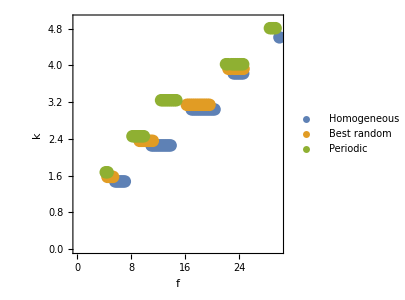

```mathematica
Clear[mins]
Clear[maxes]
filebases={"sweeps/nr8","sweeps/nr10"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
filebase="sweeps/r5";
random=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,500}],{}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6]&/@random)[[All,All,5]]]]];
means[case_]:=Mean/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(means/@wavenumbers[[2;;4]])-(means/@wavenumbers[[1;;3]]);
shifts=Transpose[#-gaps[[All,1]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->{-1,5}]
DeleteCases[Reverse[SortBy[seeds,shifts[[3,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]]
DeleteCases[Reverse[SortBy[seeds,shifts[[2,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]]
DeleteCases[Reverse[SortBy[seeds,Mean[shifts[[2;;3,First@FirstPosition[seeds,#]]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]]
m=133;
Differences[Mean[Cases[sweeps[[1]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==#][[All,1]]]&/@wavenumbers[[1;;4]]]
Differences[Mean[Cases[sweeps[[2]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==#][[All,1]]]&/@wavenumbers[[1;;4]]]
Differences[Mean[Cases[random[[m]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==#][[All,1]]]&/@wavenumbers[[1;;4]]]
gaps[[All,m]]
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[sweeps[[1]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[m]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[sweeps[[2]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{0,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Periodic"}]
```

{1.5708,2.35619,3.14159,3.92699,4.71239}

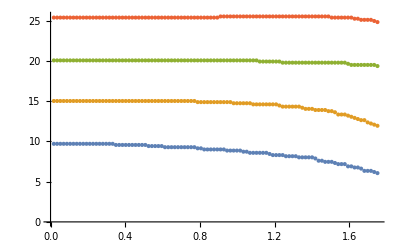

```mathematica
(*Find the gaps between tongues here, and plot as a function of samp *)
filebase="sweeps/sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
wavenumbers=DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6]&/@fsweeps)[[All,All,5]]]]
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers[[1;;4]]}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers[[1;;4]]}];
means=(mins+maxes)/2;
ListPlot[means]
```

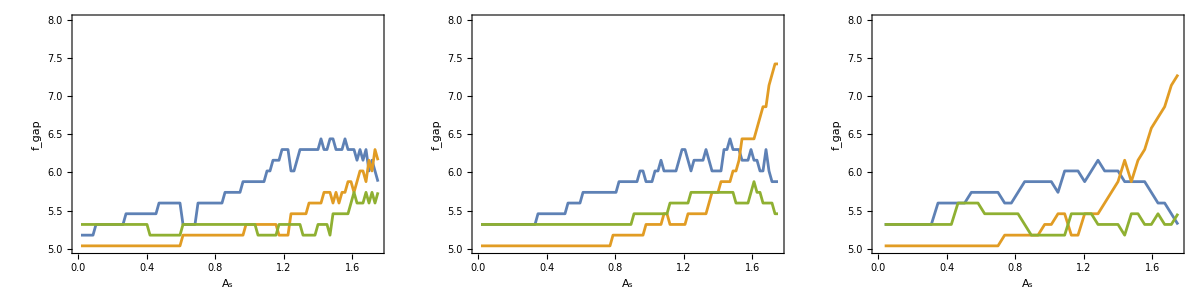

```mathematica
filebase="sweeps/sa2";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p1=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];

filebase="sweeps/sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p2=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];

filebase="sweeps/sa4";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p3=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];
Grid[{{p1,p2,p3}}]
```

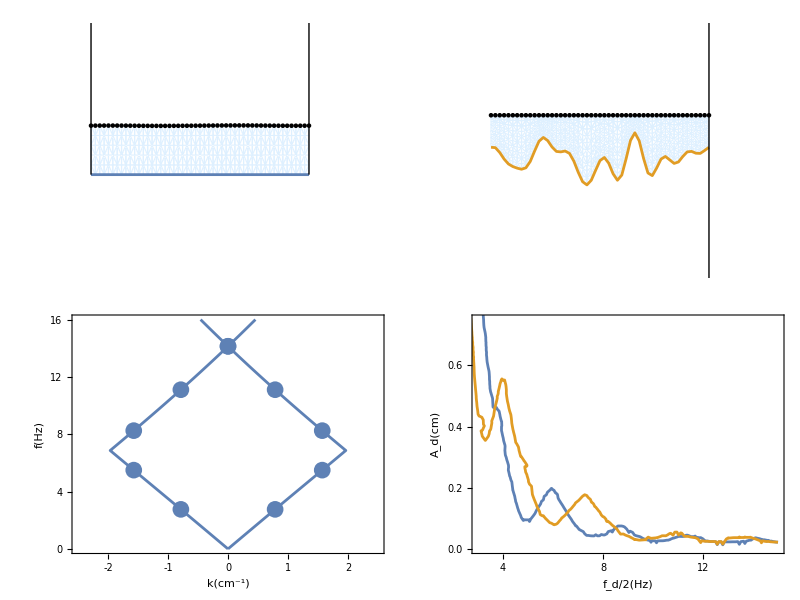

plots/randomrectanglegap.pdf

```mathematica
gap=2*Pi/length*5/4;
ks=2*gap;
hs=0.4;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-2,2,1}],Table[{i,""},{i,-2,2,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]]];
filebases={"sweeps/sr3","sweeps/r2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];p3=Show@@Table[ContourPlot[interpolations[f,a][[i]],{f,2.63,15},{a,0.000552,1.8},Contours->{0.0},PlotRange->{{3,15},{0,0.75}},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.6,0.2}],Table[{i,""},{i,0,0.6,0.2}]},{Table[{i,i},{i,4,14,2}],Table[{i,""},{i,4,14,2}]}}],{i,1,Length[sweeps]}];
filebase="data/rectanglerandom";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,1.75},{0,2.0}}],Line[{{length,-1.75},{length,2.0}}]}];
filebase="data/rectanglehomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=-1;
mesh2=mesh[[m]];
p4=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,2.0}}],Line[{{length,0},{length,2.0}}]}];
filebase="sweeps/sa4";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p5=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->150,AspectRatio->1,PlotRange->{5,8},PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[4]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[5]]]}];
p=Grid[{{p4,p2},{p1,Show[p3,Epilog->Inset[p5,{10,0.4}]]}}]
Export["plots/randomrectanglegap.pdf",p]
```

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

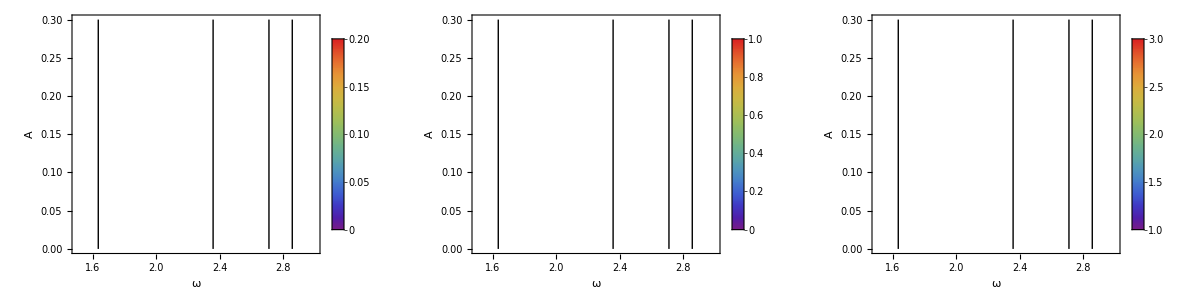

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```